```mathematica
1/4 ∫_0^4 y^2 (y-4)^2 ⅆy
```

128/15

```mathematica
1/2 ∫_0^4 y^2 (y-4)^2 Cos[(π n y)/4]ⅆy
```

-(1024 (6 n π+6 n π Cos[n π]+(-12+n^2 π^2) Sin[n π]))/(n^5 π^5)

```mathematica
FullSimplify[%,Assumptions->n∈Integers]
```

-(6144 (1+(-1)^n))/(n^4 π^4)

```mathematica
v[x_, y_, z_] := x + 128/15* Sinh[Pi/6(2 - x)]/Sinh[Pi/3]*Cos[(Pi z)/6] +
 Sinh[(5 Pi)/4 x]/Sinh[(5 Pi)/2]*Cos[(5 Pi y)/4] +
 Sinh[(7 Pi)/6 x]/Sinh[(7 Pi)/3]*Cos[(7 Pi z)/6] + 
Sum[768/(Pi^4 k^4)*Sinh[(Pi Sqrt[9 k^2 + 1])/6(x-2)]/Sinh[(Pi Sqrt[9 k^2 + 1])/3]*Cos[(Pi k y)/2]*Cos[(Pi z)/6],{k,1,50}]
```

```mathematica
lap = 
  D[v[x, y, z], {x, 2}] +
  D[v[x, y, z], {y, 2}] +
  D[v[x, y, z], {z, 2}]
```

0

```mathematica
{
D[v[x,y,z],y]/. y->0,
D[v[x,y,z],y]/. y->4,
D[v[x,y,z],z]/. z->0,
D[v[x,y,z],z]/. z->6
}
```

{0,0,0,0}

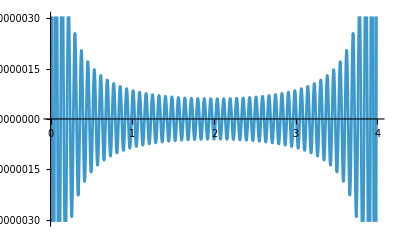

```mathematica
f0=y^2 (y-4)^2 Cos[Pi z/6];

Plot[Evaluate[v[0,y,0]-f0/. z->0],{y,0,4}]
```

```mathematica
v[2,y,z]-(Cos[5 Pi y/4]+Cos[7 Pi z/6]+2)
```

0

```mathematica
grad := Evaluate[-Grad[v[x,y,z], {x,y,z}]];
VectorPlot3D[
grad,
 {x,0,2} ,{y,0,4},{z,0,6},
AxesLabel->{"x","y","z"},
PlotLabel->"Magnetic field intensity H"
]
```

-Graphics3D-

```mathematica
hx[x_,y_,z_]:=-D[v[x,y,z],x];
hy[x_,y_,z_]:=-D[v[x,y,z],y];
hz[x_,y_,z_]:=-D[v[x,y,z],z];

StreamPlot3D[{hx[x,y,z],hy[x,y,z],hz[x,y,z]},
{x,0,2},{y,0,4},{z,0,6},
StreamPoints->Fine,StreamScale->Medium,
PlotRange->All,
AxesLabel->{"x","y","z"},
BoxRatios->{2,4,6},
PlotLabel->"Magnetic field lines"
]
```

-Graphics3D-

$Aborted